```mathematica
ClearAll["Global`*"]
```

```mathematica
(*eqnP = (w*bPred1*P*C1 +(1-w)* bPred2*P*C2) - μPred*P/.{bPred1->bPred[M],bPred2->bPred[ϕ*M],μPred->μPred[M]}; (*,σPred->σPred[M],kC->kCons[M],Sub->Sub[M]*)
eqnC1 = λ1*(R/(k/2+R))*C1-( σ1*(1-R/k)+μ1+w*b1*P)*C1/.{k->kRes,λ1->λ[M],μ1->μ[M],σ1->σ[M],b1->b[M]};
eqnC2 = λ2*(R/(k/2+R))*C2-( σ2*(1-R/k)+μ2+(1-w)*b2*P)*C2/.{k->kRes,λ2->λ[ϕ*M],μ2->μ[ϕ*M],σ2->σ[ϕ*M],b2->b[ϕ*M]};
eqnR = α*R*(1-R/(k))-( λ1/Y1*(R/(k/2+R)))*C1-( λ2/Y2*(R/(k/2+R)))*C2/.{k->kRes,λ1->λ[M],Y1->Y[M],λ2->λ[ϕ*M],Y2->Y[ϕ*M]};
LVSS = FullSimplify[Solve[{0==eqnP,0==eqnC1,0==eqnC2,0==eqnR},{P,C1,C2,R}]];*)



eqnP = (w*bPred1*P*C1 +(1-w)* bPred2*P*C2) - μPred*P/.{bPred1->bPred1[Mp],bPred2->bPred2[Mp],μPred->μPred[Mp]}; (*,σPred->σPred[M],kC->kCons[M],Sub->Sub[M]*)
eqnC1 = λ1*(R/(k/2+R))*C1-( σ1*(1-R/k)+μ1+w*bmort1*P)*C1/.{k->kRes,λ1->λ1[Mp],μ1->μ1[Mp],σ1->σ1[Mp],bmort1->bmort1[Mp]};
eqnC2 = λ2*(R/(k/2+R))*C2-( σ2*(1-R/k)+μ2+(1-w)*bmort2*P)*C2/.{k->kRes,λ2->λ2[Mp],μ2->μ2[Mp],σ2->σ2[Mp],bmort2->bmort2[Mp]};
eqnR = α*R*(1-R/(k))-( λ1/Y1*(R/(k/2+R)))*C1-( λ2/Y2*(R/(k/2+R)))*C2/.{k->kRes,λ1->λ1[Mp],Y1->Y1[Mp],λ2->λ2[Mp],Y2->Y2[Mp]};
LVSS = FullSimplify[Solve[{0==eqnP,0==eqnC1,0==eqnC2,0==eqnR},{P,C1,C2,R}]];
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/TwoPreySolutions_predpersp.m"}],LVSS]
```

/Users/justinyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/data/TwoPreySolutions_predpersp.m

```mathematica
LVSS = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/TwoPreySolutions_predpersp.m"}]];
```

```mathematica
Length[LVSS]
```

14

```mathematica
(*Internal Fixed Point*)
Psol = P/.LVSS[[13]]
C1sol = C1/.LVSS[[13]]
C2sol=C2/.LVSS[[13]]
Rsol = R/.LVSS[[13]]
(*Boundary Fixed Points*)
PsolC1only = P/.LVSS[[10]];
C1solC1only = C1/.LVSS[[10]];
C2solC1only=C2/.LVSS[[10]];
RsolC1only = R/.LVSS[[10]];

PsolC2only = P/.LVSS[[12]];
C1solC2only = C1/.LVSS[[12]];
C2solC2only=C2/.LVSS[[12]];
RsolC2only = R/.LVSS[[12]];
```

(kRes (-1+w) bmort2[Mp] (-σ1[Mp] (2 λ1[Mp] (λ2[Mp]-2 μ2[Mp])+λ2[Mp] (2 μ1[Mp]+3 σ1[Mp]))+λ1[Mp] (2 λ1[Mp]-2 μ1[Mp]+3 σ1[Mp]) σ2[Mp])+kRes w bmort1[Mp] (2 λ2[Mp] (-λ2[Mp]+μ2[Mp]) σ1[Mp]+(2 λ1[Mp] (λ2[Mp]+μ2[Mp])-λ2[Mp] (4 μ1[Mp]+3 σ1[Mp])) σ2[Mp]+3 λ1[Mp] σ2[Mp]^2)+λ2[Mp] σ1[Mp] √(kRes^2 (8 ((-1+w) bmort2[Mp] σ1[Mp]+w bmort1[Mp] σ2[Mp]) ((-1+w) bmort2[Mp] (μ1[Mp]+σ1[Mp])+w bmort1[Mp] (μ2[Mp]+σ2[Mp]))+((-1+w) bmort2[Mp] (2 λ1[Mp]-2 μ1[Mp]-σ1[Mp])-w bmort1[Mp] (-2 λ2[Mp]+2 μ2[Mp]+σ2[Mp]))^2))-λ1[Mp] σ2[Mp] √(kRes^2 (8 ((-1+w) bmort2[Mp] σ1[Mp]+w bmort1[Mp] σ2[Mp]) ((-1+w) bmort2[Mp] (μ1[Mp]+σ1[Mp])+w bmort1[Mp] (μ2[Mp]+σ2[Mp]))+((-1+w) bmort2[Mp] (2 λ1[Mp]-2 μ1[Mp]-σ1[Mp])-w bmort1[Mp] (-2 λ2[Mp]+2 μ2[Mp]+σ2[Mp]))^2)))/(4 kRes ((-1+w) bmort2[Mp] λ1[Mp]+w bmort1[Mp] λ2[Mp]) ((-1+w) bmort2[Mp] σ1[Mp]+w bmort1[Mp] σ2[Mp]))

(Y1[Mp] ((-1+w)^2 bmort2[Mp]^2 (4 λ2[Mp] μPred[Mp] σ1[Mp]^2+kRes (-1+w) α bPred2[Mp] Y2[Mp] (-2 (λ1[Mp]-μ1[Mp])^2+(λ1[Mp]-3 μ1[Mp]) σ1[Mp]))+(-1+w) bmort2[Mp] (w bmort1[Mp] (8 λ2[Mp] μPred[Mp] σ1[Mp] σ2[Mp]+kRes (-1+w) α bPred2[Mp] Y2[Mp] (-4 μ1[Mp] μ2[Mp]-3 μ2[Mp] σ1[Mp]+λ2[Mp] (4 μ1[Mp]+σ1[Mp])-3 μ1[Mp] σ2[Mp]+λ1[Mp] (-4 λ2[Mp]+4 μ2[Mp]+σ2[Mp])))+(-1+w) α bPred2[Mp] Y2[Mp] (λ1[Mp]-μ1[Mp]) √(kRes^2 ((-1+w)^2 bmort2[Mp]^2 (4 λ1[Mp]^2-4 λ1[Mp] (2 μ1[Mp]+σ1[Mp])+(2 μ1[Mp]+3 σ1[Mp])^2)+w^2 bmort1[Mp]^2 (4 λ2[Mp]^2-4 λ2[Mp] (2 μ2[Mp]+σ2[Mp])+(2 μ2[Mp]+3 σ2[Mp])^2)+2 (-1+w) w bmort1[Mp] bmort2[Mp] (-2 λ2[Mp] (2 μ1[Mp]+σ1[Mp])+(2 μ1[Mp]+3 σ1[Mp]) (2 μ2[Mp]+3 σ2[Mp])+λ1[Mp] (4 λ2[Mp]-2 (2 μ2[Mp]+σ2[Mp]))))))+w bmort1[Mp] (w bmort1[Mp] (4 λ2[Mp] μPred[Mp] σ2[Mp]^2+kRes (-1+w) α bPred2[Mp] Y2[Mp] (-2 (λ2[Mp]-μ2[Mp])^2+(λ2[Mp]-3 μ2[Mp]) σ2[Mp]))+(-1+w) α bPred2[Mp] Y2[Mp] (λ2[Mp]-μ2[Mp]) √(kRes^2 ((-1+w)^2 bmort2[Mp]^2 (4 λ1[Mp]^2-4 λ1[Mp] (2 μ1[Mp]+σ1[Mp])+(2 μ1[Mp]+3 σ1[Mp])^2)+w^2 bmort1[Mp]^2 (4 λ2[Mp]^2-4 λ2[Mp] (2 μ2[Mp]+σ2[Mp])+(2 μ2[Mp]+3 σ2[Mp])^2)+2 (-1+w) w bmort1[Mp] bmort2[Mp] (-2 λ2[Mp] (2 μ1[Mp]+σ1[Mp])+(2 μ1[Mp]+3 σ1[Mp]) (2 μ2[Mp]+3 σ2[Mp])+λ1[Mp] (4 λ2[Mp]-2 (2 μ2[Mp]+σ2[Mp]))))))))/(4 ((-1+w) bPred2[Mp] Y2[Mp] λ1[Mp]+w bPred1[Mp] Y1[Mp] λ2[Mp]) ((-1+w) bmort2[Mp] σ1[Mp]+w bmort1[Mp] σ2[Mp])^2)

(Y2[Mp] (-4 λ1[Mp] μPred[Mp] ((-1+w) bmort2[Mp] σ1[Mp]+w bmort1[Mp] σ2[Mp])^2-w α bmort2[Mp] bPred1[Mp] Y1[Mp] λ1[Mp] √(kRes^2 (8 ((-1+w) bmort2[Mp] σ1[Mp]+w bmort1[Mp] σ2[Mp]) ((-1+w) bmort2[Mp] (μ1[Mp]+σ1[Mp])+w bmort1[Mp] (μ2[Mp]+σ2[Mp]))+((-1+w) bmort2[Mp] (2 λ1[Mp]-2 μ1[Mp]-σ1[Mp])-w bmort1[Mp] (-2 λ2[Mp]+2 μ2[Mp]+σ2[Mp]))^2))+w^2 α bmort2[Mp] bPred1[Mp] Y1[Mp] λ1[Mp] √(kRes^2 (8 ((-1+w) bmort2[Mp] σ1[Mp]+w bmort1[Mp] σ2[Mp]) ((-1+w) bmort2[Mp] (μ1[Mp]+σ1[Mp])+w bmort1[Mp] (μ2[Mp]+σ2[Mp]))+((-1+w) bmort2[Mp] (2 λ1[Mp]-2 μ1[Mp]-σ1[Mp])-w bmort1[Mp] (-2 λ2[Mp]+2 μ2[Mp]+σ2[Mp]))^2))+w^2 α bmort1[Mp] bPred1[Mp] Y1[Mp] λ2[Mp] √(kRes^2 (8 ((-1+w) bmort2[Mp] σ1[Mp]+w bmort1[Mp] σ2[Mp]) ((-1+w) bmort2[Mp] (μ1[Mp]+σ1[Mp])+w bmort1[Mp] (μ2[Mp]+σ2[Mp]))+((-1+w) bmort2[Mp] (2 λ1[Mp]-2 μ1[Mp]-σ1[Mp])-w bmort1[Mp] (-2 λ2[Mp]+2 μ2[Mp]+σ2[Mp]))^2))+w α bmort2[Mp] bPred1[Mp] Y1[Mp] μ1[Mp] √(kRes^2 (8 ((-1+w) bmort2[Mp] σ1[Mp]+w bmort1[Mp] σ2[Mp]) ((-1+w) bmort2[Mp] (μ1[Mp]+σ1[Mp])+w bmort1[Mp] (μ2[Mp]+σ2[Mp]))+((-1+w) bmort2[Mp] (2 λ1[Mp]-2 μ1[Mp]-σ1[Mp])-w bmort1[Mp] (-2 λ2[Mp]+2 μ2[Mp]+σ2[Mp]))^2))-w^2 α bmort2[Mp] bPred1[Mp] Y1[Mp] μ1[Mp] √(kRes^2 (8 ((-1+w) bmort2[Mp] σ1[Mp]+w bmort1[Mp] σ2[Mp]) ((-1+w) bmort2[Mp] (μ1[Mp]+σ1[Mp])+w bmort1[Mp] (μ2[Mp]+σ2[Mp]))+((-1+w) bmort2[Mp] (2 λ1[Mp]-2 μ1[Mp]-σ1[Mp])-w bmort1[Mp] (-2 λ2[Mp]+2 μ2[Mp]+σ2[Mp]))^2))-w^2 α bmort1[Mp] bPred1[Mp] Y1[Mp] μ2[Mp] √(kRes^2 (8 ((-1+w) bmort2[Mp] σ1[Mp]+w bmort1[Mp] σ2[Mp]) ((-1+w) bmort2[Mp] (μ1[Mp]+σ1[Mp])+w bmort1[Mp] (μ2[Mp]+σ2[Mp]))+((-1+w) bmort2[Mp] (2 λ1[Mp]-2 μ1[Mp]-σ1[Mp])-w bmort1[Mp] (-2 λ2[Mp]+2 μ2[Mp]+σ2[Mp]))^2))+kRes w α bPred1[Mp] Y1[Mp] ((-1+w)^2 bmort2[Mp]^2 (-2 (λ1[Mp]-μ1[Mp])^2+(λ1[Mp]-3 μ1[Mp]) σ1[Mp])+w^2 bmort1[Mp]^2 (-2 (λ2[Mp]-μ2[Mp])^2+(λ2[Mp]-3 μ2[Mp]) σ2[Mp])+(-1+w) w bmort1[Mp] bmort2[Mp] (-4 μ1[Mp] μ2[Mp]-3 μ2[Mp] σ1[Mp]+λ2[Mp] (4 μ1[Mp]+σ1[Mp])-3 μ1[Mp] σ2[Mp]+λ1[Mp] (-4 λ2[Mp]+4 μ2[Mp]+σ2[Mp])))))/(4 ((-1+w) bPred2[Mp] Y2[Mp] λ1[Mp]+w bPred1[Mp] Y1[Mp] λ2[Mp]) ((-1+w) bmort2[Mp] σ1[Mp]+w bmort1[Mp] σ2[Mp])^2)

(-kRes (-1+w) bmort2[Mp] (2 λ1[Mp]-2 μ1[Mp]-σ1[Mp])+kRes w bmort1[Mp] (-2 λ2[Mp]+2 μ2[Mp]+σ2[Mp])+√(kRes^2 (8 ((-1+w) bmort2[Mp] σ1[Mp]+w bmort1[Mp] σ2[Mp]) ((-1+w) bmort2[Mp] (μ1[Mp]+σ1[Mp])+w bmort1[Mp] (μ2[Mp]+σ2[Mp]))+((-1+w) bmort2[Mp] (2 λ1[Mp]-2 μ1[Mp]-σ1[Mp])-w bmort1[Mp] (-2 λ2[Mp]+2 μ2[Mp]+σ2[Mp]))^2)))/(4 (-1+w) bmort2[Mp] σ1[Mp]+4 w bmort1[Mp] σ2[Mp])

What are the solutions if the predator is specializing on C1? (w->1)

```mathematica
PsolNoC2= FullSimplify[Psol/.w->1]
C1solNoC2= FullSimplify[C1sol/.w->1]
C2solNoC2= FullSimplify[C2sol/.w->1]
RsolNoC2 = FullSimplify[Rsol/.w->1]
```

1/(4 kRes bmort1[Mp]^2 λ2[Mp] σ2[Mp])(kRes bmort1[Mp] (2 λ2[Mp] (-λ2[Mp]+μ2[Mp]) σ1[Mp]+(2 λ1[Mp] (λ2[Mp]+μ2[Mp])-λ2[Mp] (4 μ1[Mp]+3 σ1[Mp])) σ2[Mp]+3 λ1[Mp] σ2[Mp]^2)+(λ2[Mp] σ1[Mp]-λ1[Mp] σ2[Mp]) √(kRes^2 bmort1[Mp]^2 (4 λ2[Mp]^2-4 λ2[Mp] (2 μ2[Mp]+σ2[Mp])+(2 μ2[Mp]+3 σ2[Mp])^2)))

μPred[Mp]/bPred1[Mp]

(Y2[Mp] (α bPred1[Mp] Y1[Mp] (λ2[Mp]-μ2[Mp]) √(kRes^2 bmort1[Mp]^2 (4 λ2[Mp]^2-4 λ2[Mp] (2 μ2[Mp]+σ2[Mp])+(2 μ2[Mp]+3 σ2[Mp])^2))+bmort1[Mp] (-4 λ1[Mp] μPred[Mp] σ2[Mp]^2+kRes α bPred1[Mp] Y1[Mp] (-2 (λ2[Mp]-μ2[Mp])^2+(λ2[Mp]-3 μ2[Mp]) σ2[Mp]))))/(4 bmort1[Mp] bPred1[Mp] Y1[Mp] λ2[Mp] σ2[Mp]^2)

(kRes bmort1[Mp] (-2 λ2[Mp]+2 μ2[Mp]+σ2[Mp])+√(kRes^2 bmort1[Mp]^2 (8 σ2[Mp] (μ2[Mp]+σ2[Mp])+(-2 λ2[Mp]+2 μ2[Mp]+σ2[Mp])^2)))/(4 bmort1[Mp] σ2[Mp])

```mathematica
JacobianFullModel=({
{D[eqnP,P],D[eqnP,C1],D[eqnP,C2],D[eqnP,R]},
{D[eqnC1,P],D[eqnC1,C1],D[eqnC1,C2],D[eqnC1,R]},
{D[eqnC2,P],D[eqnC2,C1],D[eqnC2,C2],D[eqnC2,R]},
{D[eqnR,P],D[eqnR,C1],D[eqnR,C2],D[eqnR,R]}})/.{P->Psol,C1->C1sol,C2->C2sol,R->Rsol};
```

```mathematica
data = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/densitydata.csv"}],"csv"];
carnivoredata = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/carnivoredensities_trimmed.csv"}],"csv"];
```

***Declare Metabolic Parameters***

```mathematica
NotebookEvaluate[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/src/metabolic_constants.nb"}]];
```

***Declare Allometric Functions - SPECIFIC TO MODEL AND PERSPECTIVE***

```mathematica
NotebookEvaluate[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/src/allometric_functions_predpersp.nb"}]];
```

***Declare PPMR***

```mathematica
NotebookEvaluate[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/src/ppmr_primary.nb"}]];
```

Check Original Model w/o predation... do we get pretty close to the Damuth Data without predation?
1/19/2023 - mass Coordinates for C2 are now converted to M2 units in the plot (where M2 = M1/ϕ)... so instead of a particular feature on the C2 curve relating to the mass of consumer 1, it now relates to the mass of consumer 2. So the x-axis is just ‘Consumer mass’, each C1 and C2 curve relating to M1 and M2, respectively.

```mathematica
PercentGrowthConsumer1=0.8; (*Percent with which the predator relies on Consumer 1 for food*)
ScaledMassConsumer2 =0.9; (*Proportional size of Consumer 2 with respect to Consumer 1 (focal)*)
C1DensityList=ParallelTable[{10^i,((1/OptPreyMass[Mp])*C1sol/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2})/.Mp->10^i},{i,1,8,0.01}];
C1DensityListConsMass = Transpose[{OptPreyMass[ C1DensityList[[All,1]]],C1DensityList[[All,2]]}];
C2DensityList=ParallelTable[{10^i,((1/(ϕ*OptPreyMass[Mp]))*C2sol/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2})/.Mp->10^i},{i,1,8,0.01}];
C2DensityListConsMass = Transpose[{OptPreyMass[ ϕ*C2DensityList[[All,1]]],C2DensityList[[All,2]]}];
```

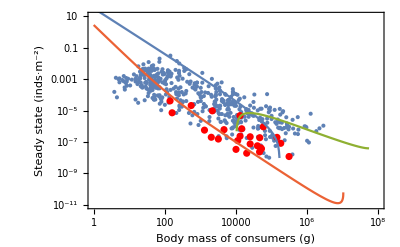

```mathematica
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,10}},Frame->True,FrameLabel->{"Body mass of consumers (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
(*LogLogPlot[(1/OptPreyMass[Mp])*C1sol/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{Mp,1,10^8},Frame->True,PlotStyle->ColorData[97,1]],
LogLogPlot[(((1/(ϕ*OptPreyMass[Mp]))*C2sol))/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{Mp,1,10^8},Frame->True,PlotStyle->ColorData[97,3]],*)
ListLogLogPlot[C1DensityListConsMass,Joined->True,PlotStyle->ColorData[97,1]],
ListLogLogPlot[C2DensityListConsMass/.ϕ->ScaledMassConsumer2,Joined->True,PlotStyle->ColorData[97,3]],
LogLogPlot[(1/Mp)*Psol/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{Mp,1,10^8},Frame->True,PlotStyle->ColorData[97,4]]
}]
```

Detect population thresholds, where the density plummets to zero

```mathematica
(*RealQ[x_]:=Element[x,Reals]===True;*)
RealQ[x_]:=(Im[x]==0)===True; (*THIS WORKS BETTER*)
DetectThresholdLowest[DensitySol_,wvalue_,phivalue_]:=
Module[{Sol = DensitySol},
DiscreteDensityTable = Table[{10^i,(Sol/.{w->wvalue,ϕ->phivalue})/.Mass->10^i},{i,0,7.5,0.05}];
SlopesOfLogs=Transpose[{DiscreteDensityTable[[1;;(Length[DiscreteDensityTable[[All,1]]]-1),1]],Differences[Log[DiscreteDensityTable[[All,2]]]]/Differences[Log[DiscreteDensityTable[[All,1]]]]}];
RealSlopesOfLogsPos =  Flatten[Position[SlopesOfLogs[[All,2]],_?(RealQ[#]&)],1];
RealSlopesOfLogs=SlopesOfLogs[[RealSlopesOfLogsPos]];
(*MinDensity=10^-8;*)
ThresholdDensityPos = Flatten[Position[RealSlopesOfLogs[[All,2]],_?(#==Max[RealSlopesOfLogs[[All,2]]]&)],1];
If[Length[ThresholdDensityPos]>0,
RealSlopesOfLogs[[ThresholdDensityPos[[1]],1]],
Missing[]
]
];
DetectThreshold[DensitySol_,wvalue_,phivalue_]:=
Module[{Sol= DensitySol},
diffSol = Transpose[{Table[10^i,{i,0,7.5-0.01,0.01}],Differences[Table[Abs[(Sol)/.{w->wvalue,ϕ->phivalue}]/.Mass->10^i,{i,0,7.5,0.01}]]*Table[10^i,{i,0,7.5-0.01,0.01}]}];
diffSolMultDiff = Transpose[{Table[10^i,{i,0,7.5-0.02,0.01}],Differences[diffSol[[All,2]]]}];
FirstNegative =Flatten[Position[diffSolMultDiff[[All,2]],_?(#<0&)],1];

(*intvecSol = Intersection[Flatten[Position[diffSol[[All,1]],_?((#>0)&)],1],
Flatten[Position[diffSol[[All,2]],_?(#>0&)],1]];*)
(*intvecSol =Flatten[Position[diffSol[[All,2]],_?(#>0&)],1];*)
(*thresholdpositionC = If[Length[intvecC]==0,Length[diffC],intvecC[[1]]];
thresholdsizeC =  diffC[[thresholdpositionC]][[1]];*)

(*Test to see if there is a threshold at all*)
If[Length[FirstNegative]==0,
Missing[],
thresholdsizeSol = diffSol[[FirstNegative[[1]]]][[1]];
DensityAtMass = (DensitySol/.{w->wvalue,ϕ->phivalue,Mass->thresholdsizeSol*(1-0)});
DensityAtMassLow = (DensitySol/.{w->wvalue,ϕ->phivalue,Mass->thresholdsizeSol*(1-0.1)});
DensityAtMassHigh = (DensitySol/.{w->wvalue,ϕ->phivalue,Mass->thresholdsizeSol*(1+0.1)});
(*Test to make sure it is non-negative and non-imaginary*)
If[(Re[DensityAtMassLow]>0 &&RealQ[DensityAtMassLow])||(Re[DensityAtMassHigh] > 0&&RealQ[DensityAtMassHigh]),
(*Test to make sure it is an extinction threshold, where density -> 0*)
If[Re[DensityAtMass]<Re[DensityAtMassLow]||Re[DensityAtMass]<Re[DensityAtMassHigh],
thresholdsizeSol,
Missing[]
],
Missing[]
]
]
(*thresholdsizeSol*)
];
```

```mathematica
C1solMass = ((1/M)*C1sol)/.M->Mass;
C2solMass = ((1/(ϕ*M))*C2sol)/.{M->Mass/ϕ};
PsolMass = ((1/OptPredMass[M])*Psol)/.{M->Mass};
```

```mathematica
DetectThresholdLowest[C1solMass,PercentGrowthConsumer1,ScaledMassConsumer2]
```

707946.

```mathematica
DetectThreshold[C2solMass,PercentGrowthConsumer1,ScaledMassConsumer2]
```

2818.38

Allow w and ϕ to vary, and calculate:
1) The C1 threshold mass (if it exists)
2) The C2 threshold mass (if it exists)
3) The difference in mass from C2 to C1 where 3 populations co-exist (if it exists)

```mathematica
(*wvalues = Table[i,{i,0.01,0.99,0.01}];
phivalues = Table[i,{i,0.01,0.99,0.01}];*)
```

```mathematica
wvalues = Table[i,{i,0.01,0.99,0.02}];
phivalues = Table[i,{i,0.01,0.99,0.02}];
C1Thresholds = Flatten[ParallelTable[
{wvalues[[i]],phivalues[[j]],DetectThresholdLowest[C1solMass,wvalues[[i]],phivalues[[j]]]},
{i,1,Length[wvalues]},{j,1,Length[phivalues]}],1];
C2Thresholds = Flatten[ParallelTable[
{wvalues[[i]],phivalues[[j]],DetectThresholdLowest[C2solMass,wvalues[[i]],phivalues[[j]]]},
{i,1,Length[wvalues]},{j,1,Length[phivalues]}],1];
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/thresholdsC1C2overWPhi_HaywardLogit.m"}],{C1Thresholds,C2Thresholds}]
```

/Users/jdyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/data/thresholdsC1C2overWPhi_HaywardLogit.m

```mathematica
(*C1C2ThresholdData = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/thresholdsC1C2overWPhi_HaywardLogit.m"}]];
C1Thresholds=C1C2ThresholdData[[1]];
C2Thresholds=C1C2ThresholdData[[2]];*)
```

```mathematica
(*C1C2Thresholds = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/thresholdsC1C2overWPhi_HaywardLogit.m"}]];
C1Thresholds = C1C2Thresholds[[1]];
C2Thresholds = C1C2Thresholds[[2]];*)
```

```mathematica
MissingPosC1 = Flatten[Position[C1Thresholds[[All,3]],_?(#==Missing[]&)],1];
MissingPointsC1 = Transpose[{C1Thresholds[[MissingPosC1]][[All,1]],C1Thresholds[[MissingPosC1]][[All,2]]}];
MissingPosC2 = Flatten[Position[C2Thresholds[[All,3]],_?(#==Missing[]&)],1];
MissingPointsC2 = Transpose[{C2Thresholds[[MissingPosC2]][[All,1]],C2Thresholds[[MissingPosC2]][[All,2]]}];
```

```mathematica
logTicks[min_,max_]:={#,10^#}&/@FindDivisions[{min,max},5]
```

```mathematica
logTicks[1,7]
```

{{0,1},{2,100},{4,10000},{6,1000000},{8,100000000}}

```mathematica
N[Log10[3*10^7]]
```

7.47712

```mathematica
(*Only way I can think of to force even scales*)
C1Thresholds[[1,3]]=10;
MaxMass = 3.019951720402019*^7;
ThresholdPlot=GraphicsRow[{
Show[{
ListContourPlot[C1Thresholds,FrameLabel->{"Proportional growth from Consumer 1","Proportional size of Consumer 2"},ScalingFunctions->{None,None,"Log"},LabelStyle->Directive[FontSize->16],PlotLegends->BarLegend[{ColorData[{"SandyTerrain","Reverse"}],{Log10[10],Log10[MaxMass]}},Ticks->logTicks[1,Log10[MaxMass]],LegendLabel->"C_1^† thresh."],ColorFunction->ColorData[{"SandyTerrain","Reverse"}],PlotRange->{10,MaxMass},Contours->20,ContourStyle->None],
(*ListPlot[MissingPointsC1],*)
Graphics[{White,Opacity[1],ConcaveHullMesh[MissingPointsC1,0.02,All]}]
},ImageSize->350],
Show[{
ListContourPlot[C2Thresholds,FrameLabel->{"Proportional growth from Consumer 1","Proportional size of Consumer 2"},ScalingFunctions->{None,None,"Log"},LabelStyle->Directive[FontSize->16],PlotLegends->BarLegend[{ColorData[{"SandyTerrain","Reverse"}],{Log10[10],Log10[MaxMass]}},Ticks->logTicks[1,Log10[MaxMass]],LegendLabel->"C_2^† thresh."],ColorFunction->ColorData[{"SandyTerrain","Reverse"}],PlotRange->{10,3.019951720402019*^7},Contours->20,ContourStyle->None],
(*ListPlot[MissingPointsC2],*)
(*Graphics[{White,Opacity[1],ConcaveHullMesh[MissingPointsC2,0.01]}],*)
Graphics[{White,Opacity[1],ConcaveHullMesh[MissingPointsC1,0.02,All]}]
},ImageSize->350]
},ImageSize->1000]
```

-Graphics-

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_thresholdsC1C2_w_phi_HaywardLogit.pdf"}],ThresholdPlot]
```

/Users/jdyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_thresholdsC1C2_w_phi_HaywardLogit.pdf

```mathematica
DiffThreshold = Transpose[{C1Thresholds[[All,1]],C2Thresholds[[All,2]],C1Thresholds[[All,3]]-C2Thresholds[[All,3]]}];
```

```mathematica
Max[DiffThreshold[[Flatten[Position[DiffThreshold[[All,3]],_?(#>0&)],1],3]]]
```

Max[3.01987×10^7,10-Missing,741310.-Missing,977237.-Missing,1.07152×10^6-Missing,1.1749×10^6-Missing,1.31826×10^6-Missing,1.47911×10^6-Missing,1.54882×10^6-Missing,1.99526×10^6-Missing,2.81838×10^6-Missing,2.95121×10^6-Missing,3.98107×10^6-Missing,4.16869×10^6-Missing]

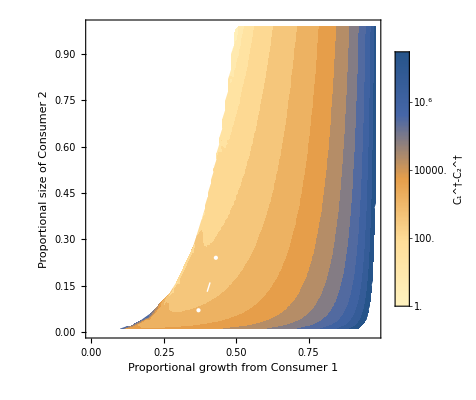

```mathematica
MaxDiff = 3.0198666065981988*^7;
DiffThresholdPlot = Show[{
ListContourPlot[DiffThreshold,FrameLabel->{"Proportional growth from Consumer 1","Proportional size of Consumer 2"},ScalingFunctions->{None,None,"Log"},LabelStyle->Directive[FontSize->16],ColorFunction->ColorData[{"M10DefaultDensityGradient","Reverse"}],PlotLegends->BarLegend[{ColorData[{"M10DefaultDensityGradient","Reverse"}],{Log10[1],Log10[MaxDiff]}},Ticks->logTicks[Log10[1],Log10[MaxDiff]],LegendLabel->"C_1^†-C_2^†"],Contours->20,ContourStyle->None,PlotRange->{1,MaxDiff}],
Graphics[{White,Opacity[1],ConcaveHullMesh[MissingPointsC1,0.02,All]}](*,
Graphics[{ColorData[97,1],Opacity[0.8],ConcaveHullMesh[MissingPointsC2,0.01]}]*)
}]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_diffthresholds_w_phi.pdf"}],DiffThresholdPlot]
```

/home/jdyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_diffthresholds_w_phi.pdf

Aside from Thresholds, what is the mass range of feasibility for P, C1, C2?

```mathematica
DetectFeasibilityRange[DensitySol_,wvalue_,phivalue_]:=
Module[{Sol= DensitySol},
MassRange = Table[10^i,{i,0,7.5,0.1}];
DensitiesOverMass =Flatten[Table[Sol/.{w->wvalue,ϕ->phivalue}/.Mass->i,{i,{MassRange}}],1];
(*Find Positive Densities*);
PositiveDensitiesPos = Flatten[Position[DensitiesOverMass,_?(Re[#]>0&&RealQ[#]&)],1];
If[Length[PositiveDensitiesPos]>0,
MaxPosMass = Last[MassRange[[PositiveDensitiesPos]]];
MinPosMass = First[MassRange[[PositiveDensitiesPos]]];
Interval[{MinPosMass,MaxPosMass}],
Interval[]
]
];
```

```mathematica
II=IntervalIntersection[
DetectFeasibilityRange[C1solMass,0.1,0.1],
DetectFeasibilityRange[C2solMass,0.1,0.1],
DetectFeasibilityRange[PsolMass,0.1,0.1]
]
```

Greater::nord: Invalid comparison with 2.06755×10^-8+6.44147×10^-8 ⅈ attempted.

Greater::nord: Invalid comparison with 7.18501×10^-9+4.19184×10^-8 ⅈ attempted.

Greater::nord: Invalid comparison with 3.19789×10^-9+2.91393×10^-8 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Interval[]

```mathematica
DensitiesOverMass =Flatten[Table[C2solMass/.{w->0.1,ϕ->0.1}/.Mass->i,{i,{MassRange}}],1]
```

{3.40962,2.51946,1.86182,1.37595,1.01695,0.751679,0.555657,0.410794,0.303731,0.224597,0.166101,0.122858,0.090886,0.0672452,0.0497625,0.0368321,0.0272673,0.0201909,0.0149548,0.0110795,0.0082109,0.00608698,0.00451407,0.00334891,0.00248556,0.00184564,0.00137118,0.00101925,0.000758122,0.000564273,0.000420301,0.000313317,0.000233772,0.000174593,0.000130534,0.000097708,0.0000732307,0.0000549626,0.000041315,0.0000311084,0.0000234664,0.0000177371,0.000013436,0.0000102021,7.76662×10^-6,5.92922×10^-6,4.54035×10^-6,3.48835×10^-6,2.68973×10^-6,2.08203×10^-6,1.61843×10^-6,1.26381×10^-6,9.91781×10^-7,7.82503×10^-7,6.21017×10^-7,4.96038×10^-7,3.99039×10^-7,3.23569×10^-7,2.64749×10^-7,2.18893×10^-7,1.83237×10^-7,1.55748×10^-7,1.35014×10^-7,1.20248×10^-7,1.11535×10^-7,1.10918×10^-7,1.28214×10^-7,2.59044×10^-7,4.06202×10^-7,2.06755×10^-8+6.44147×10^-8 ⅈ,7.18501×10^-9+4.19184×10^-8 ⅈ,3.19789×10^-9+2.91393×10^-8 ⅈ,1.50677×10^-9+2.10252×10^-8 ⅈ,6.57367×10^-10+1.5516×10^-8 ⅈ,1.86764×10^-10+1.16207×10^-8 ⅈ,-9.35384×10^-11+8.79126×10^-9 ⅈ}

```mathematica
PositiveDensitiesPos = Flatten[Position[DensitiesOverMass,_?(Re[#]>0&&RealQ[#]&)],1]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69}

```mathematica
DensitiesOverMass[[PositiveDensitiesPos]]
```

{3.40962,2.51946,1.86182,1.37595,1.01695,0.751679,0.555657,0.410794,0.303731,0.224597,0.166101,0.122858,0.090886,0.0672452,0.0497625,0.0368321,0.0272673,0.0201909,0.0149548,0.0110795,0.0082109,0.00608698,0.00451407,0.00334891,0.00248556,0.00184564,0.00137118,0.00101925,0.000758122,0.000564273,0.000420301,0.000313317,0.000233772,0.000174593,0.000130534,0.000097708,0.0000732307,0.0000549626,0.000041315,0.0000311084,0.0000234664,0.0000177371,0.000013436,0.0000102021,7.76662×10^-6,5.92922×10^-6,4.54035×10^-6,3.48835×10^-6,2.68973×10^-6,2.08203×10^-6,1.61843×10^-6,1.26381×10^-6,9.91781×10^-7,7.82503×10^-7,6.21017×10^-7,4.96038×10^-7,3.99039×10^-7,3.23569×10^-7,2.64749×10^-7,2.18893×10^-7,1.83237×10^-7,1.55748×10^-7,1.35014×10^-7,1.20248×10^-7,1.11535×10^-7,1.10918×10^-7,1.28214×10^-7,2.59044×10^-7,4.06202×10^-7}

```mathematica
RegionMeasure[II]
```

9952.62

```mathematica
IntervalSizeWPhi = ParallelTable[
C1Interval = DetectFeasibilityRange[C1solMass,wvalues[[i]],phivalues[[j]]];
C2Interval = DetectFeasibilityRange[C2solMass,wvalues[[i]],phivalues[[j]]];
PInterval = DetectFeasibilityRange[PsolMass,wvalues[[i]],phivalues[[j]]];
PC1C2Interval = IntervalIntersection[C1Interval,C2Interval,PInterval];
PC1Interval = IntervalIntersection[C1Interval,PInterval];
PC2Interval = IntervalIntersection[C2Interval,PInterval];
C1C2Interval=IntervalIntersection[C1Interval,C2Interval];
{wvalues[[i]],phivalues[[j]],RegionMeasure[C1C2Interval],RegionMeasure[PC1Interval],RegionMeasure[PC2Interval],RegionMeasure[PC1C2Interval]},
{i,1,Length[wvalues]},{j,1,Length[phivalues]}
];
```

3.16228×10^7

```mathematica
ZeroOverlapPC1C2Pos = Flatten[Position[Flatten[IntervalSizeWPhi,1][[All,6]],_?(#==0&)],1];
ZeroOverlapPC1C2Points = Transpose[{Flatten[IntervalSizeWPhi,1][[ZeroOverlapPC1C2Pos,1]],Flatten[IntervalSizeWPhi,1][[ZeroOverlapPC1C2Pos,2]]}];
```

```mathematica
ZeroOverlapPC1C2Points
```

```mathematica
PlotInterval[IntervalArray_,ColumnID_,Name_]:= Module[{IntervalSizeWPhi=IntervalArray},IntervalSizePC1C2 = Transpose[{Flatten[IntervalSizeWPhi,1][[All,1]],Flatten[IntervalSizeWPhi,1][[All,2]],Flatten[IntervalSizeWPhi,1][[All,ColumnID]]}];
MaxRange=Max[IntervalSizeWPhi[[All,ColumnID]]];
ZeroOverlapPC1C2Pos = Flatten[Position[Flatten[IntervalSizeWPhi,1][[All,ColumnID]],_?(#==0&)],1];
ZeroOverlapPC1C2Points = Transpose[{Flatten[IntervalSizeWPhi,1][[ZeroOverlapPC1C2Pos,1]],Flatten[IntervalSizeWPhi,1][[ZeroOverlapPC1C2Pos,2]]}];
Show[{
ListContourPlot[IntervalSizePC1C2,FrameLabel->{"Proportional growth from Consumer 1","Proportional size of Consumer 2"},ScalingFunctions->{None,None,"Log"},LabelStyle->Directive[FontSize->16],ColorFunction->ColorData[{"M10DefaultDensityGradient","Reverse"}],PlotLegends->BarLegend[{ColorData[{"M10DefaultDensityGradient","Reverse"}],{Log10[1],Log10[MaxRange]}},Ticks->logTicks[Log10[1],Log10[MaxDiff]],LegendLabel->Name],Contours->20,ContourStyle->None,PlotRange->{1,MaxRange}]
(*Graphics[{ColorData[97,1],Opacity[0.8],ConcaveHullMesh[MissingPointsC2,0.01]}]*)
(*ListPlot[ZeroOverlapPC1C2Points]*)
,Graphics[{ColorData[97,4],Opacity[1],ConcaveHullMesh[ZeroOverlapPC1C2Points,0.02,All]}]
,Graphics[{ColorData[97,5],Opacity[0.8],ConcaveHullMesh[MissingPointsC1,0.02,All]}]
}]
]
```

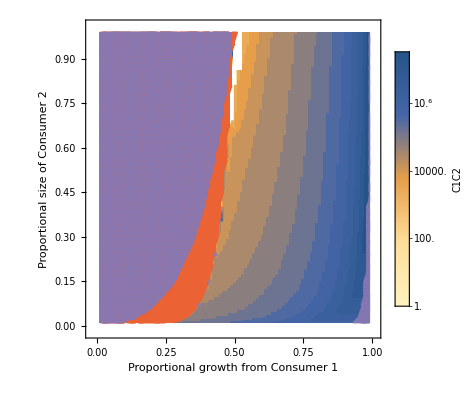

```mathematica
PlotInterval[IntervalSizeWPhi,3,"C1C2"]
```

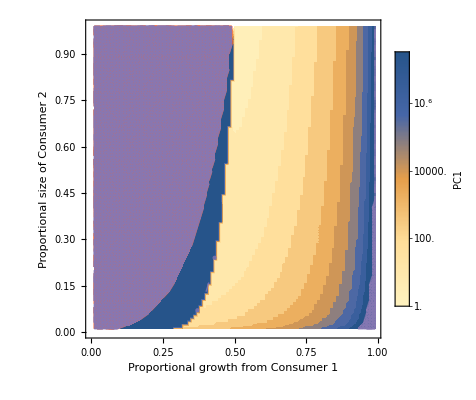

```mathematica
PlotInterval[IntervalSizeWPhi,4,"PC1"]
```

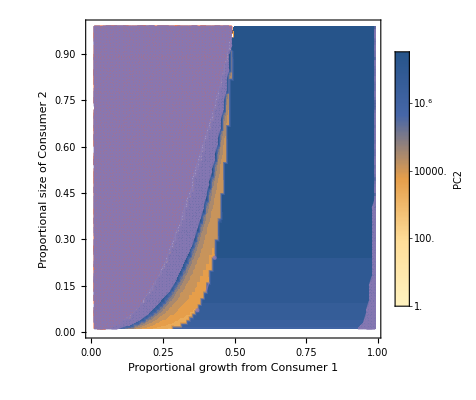

```mathematica
PlotInterval[IntervalSizeWPhi,5,"PC2"]
```

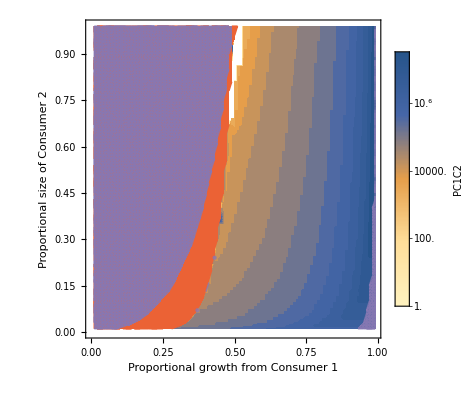

```mathematica
PlotInterval[IntervalSizeWPhi,6,"PC1C2"]
```

Define and plot Regional boundaries for different types of dynamics

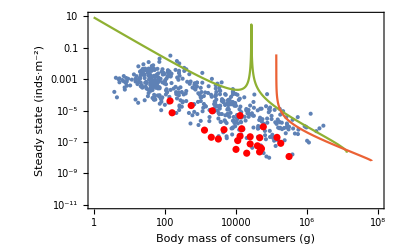

```mathematica
PercentGrowthConsumer1=0.28; (*Percent with which the predator relies on Consumer 1 for food*)
ScaledMassConsumer2 =0.2; (*Proportional size of Consumer 2 with respect to Consumer 1 (focal)*)
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,10}},Frame->True,FrameLabel->{"Body mass of consumers (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/M)*C1sol/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,1]],
LogLogPlot[(((1/(ϕ*M))*C2sol)/.{M->M2/ϕ})/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{M2,1,10^8},Frame->True,PlotStyle->ColorData[97,3]],
LogLogPlot[(1/OptPredMass[M])*Psol/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,4]]
}]
```

```mathematica
MaxRange-1000
```

3.16218×10^7

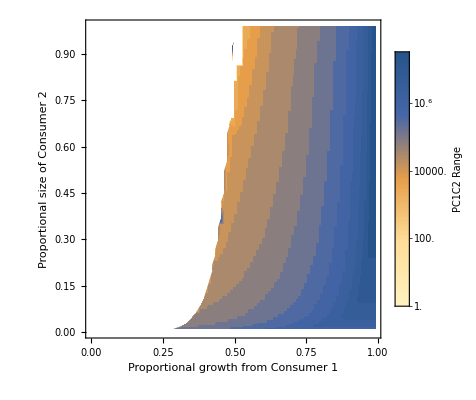

```mathematica
IntervalSizePC1C2 = Transpose[{Flatten[IntervalSizeWPhi,1][[All,1]],Flatten[IntervalSizeWPhi,1][[All,2]],Flatten[IntervalSizeWPhi,1][[All,6]]}];
MaxRange=Max[IntervalSizeWPhi[[All,6]]];
ZeroOverlapPC1C2Pos = Flatten[Position[Flatten[IntervalSizeWPhi,1][[All,6]],_?(#==0&)],1];
ZeroOverlapPC1C2Points = Transpose[{Flatten[IntervalSizeWPhi,1][[ZeroOverlapPC1C2Pos,1]],Flatten[IntervalSizeWPhi,1][[ZeroOverlapPC1C2Pos,2]]}];
Show[{
ListContourPlot[IntervalSizePC1C2,FrameLabel->{"Proportional growth from Consumer 1","Proportional size of Consumer 2"},ScalingFunctions->{None,None,"Log"},LabelStyle->Directive[FontSize->16],ColorFunction->ColorData[{"M10DefaultDensityGradient","Reverse"}],PlotLegends->BarLegend[{ColorData[{"M10DefaultDensityGradient","Reverse"}],{Log10[1],Log10[MaxRange]}},Ticks->logTicks[Log10[1],Log10[MaxDiff]],LegendLabel->"PC1C2 Range"],Contours->20,ContourStyle->None,PlotRange->{1,MaxRange}],(*,
Graphics[{White,Opacity[1],ConcaveHullMesh[MissingPointsC1,0.02,All]}],
Graphics[{ColorData[97,1],Opacity[0.8],ConcaveHullMesh[MissingPointsC2,0.01]}]*)
(*ListPlot[ZeroOverlapPC1C2Points]*)
Graphics[{White,Opacity[1],ConcaveHullMesh[ZeroOverlapPC1C2Points,0.02,All]}]
}]
```

```mathematica
Flatten[IntervalSizeWPhi,1][[1]][[3]]
```

```mathematica
(*Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,10}},Frame->True,FrameLabel->{"Body mass of focal consumer (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/M)*C1sol/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,1]],
LogLogPlot[(1/(ϕ*M))*C2sol/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,3]],
LogLogPlot[(1/OptPredMass[M])*Psol/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,4]]
}]*)
```

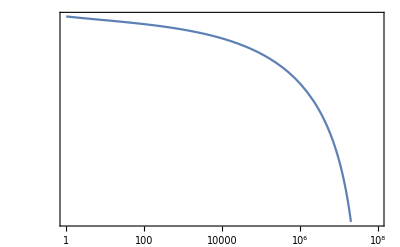

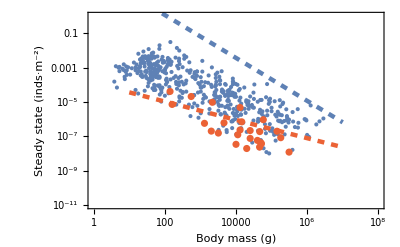

```mathematica
LogLogPlot[Rsol/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,1]]
MaxDensitiesPlot = Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->ColorData[97,4]],
LogLogPlot[(1/M)*PreyDensityTheoreticalMax[M]/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,1]}],
LogLogPlot[(1/OptPredMass[M])*PredatorDensityTheoreticalMax[OptPredMass[M],M]/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,4]}]
}]
```

Given a mass value, phi value, and w value, plot steady states

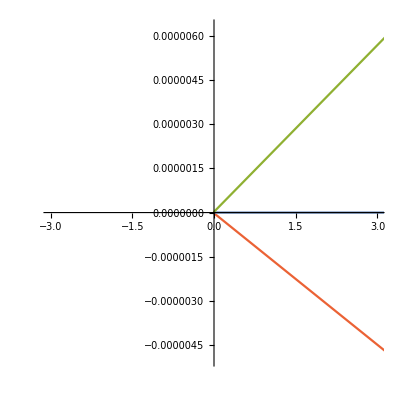

-Graphics-

```mathematica
(*MassValue = 100000;*)
PercentGrowthConsumer1=1; (*Percent with which the predator relies on Consumer 1 for food*)
ScaledMassConsumer2 =0.2; (*Proportional size of Consumer 2 with respect to Consumer 1 (focal)*)
Show[{
ParametricPlot[{(1/M)*C1sol,(1/OptPredMass[M])*Psol}/.{w->PercentGrowthConsumer1,ϕ->1.2},{M,1,10^7},AspectRatio->1,PlotRange->{{-3,3},All},PlotStyle->ColorData[97,4]],
ParametricPlot[{(1/M)*C1sol,(1/OptPredMass[M])*Psol}/.{w->PercentGrowthConsumer1,ϕ->1},{M,1,10^7},AspectRatio->1,PlotRange->All,PlotStyle->ColorData[97,1]],
ParametricPlot[{(1/M)*C1sol,(1/OptPredMass[M])*Psol}/.{w->PercentGrowthConsumer1,ϕ->0.8},{M,1,10^7},AspectRatio->1,PlotRange->All,PlotStyle->ColorData[97,3]]
}]
Show[{
ParametricPlot[{(1/(ϕ*M))*C2sol,(1/OptPredMass[M])*Psol}/.{w->PercentGrowthConsumer1,ϕ->1.2},{M,1,10^7},AspectRatio->1,PlotStyle->ColorData[97,4],ScalingFunctions->{"Log","Log"}],
ParametricPlot[{(1/(ϕ*M))*C2sol,(1/OptPredMass[M])*Psol}/.{w->PercentGrowthConsumer1,ϕ->1},{M,1,10^7},AspectRatio->1PlotStyle->ColorData[97,1],ScalingFunctions->{"Log","Log"}],
ParametricPlot[{(1/(ϕ*M))*C2sol,(1/OptPredMass[M])*Psol}/.{w->PercentGrowthConsumer1,ϕ->0.8},{M,1,10^7},AspectRatio->1,PlotStyle->ColorData[97,3],ScalingFunctions->{"Log","Log"}]
}]
```

```mathematica
v
```

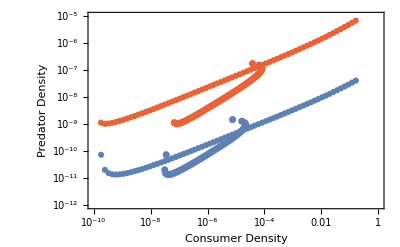

```mathematica
Show[{
ListLogLogPlot[Table[{(1/M)*C1sol,(1/OptPredMass[M])*Psol}/.{M->10^i,w->PercentGrowthConsumer1,ϕ->0.2},{i,1,8,0.1}],PlotStyle->ColorData[97,4],PlotRange->{{10^-10,10^0},{10^-12,10^-5}},Frame->True,FrameLabel->{"Consumer Density","Predator Density"}],
ListLogLogPlot[Table[{(1/(ϕ*M))*C2sol,(1/OptPredMass[M])*Psol}/.{M->10^i,w->PercentGrowthConsumer1,ϕ->0.2},{i,1,8,0.1}],PlotStyle->ColorData[97,4]],
ListLogLogPlot[Table[{(1/(ϕ*M))*C1sol,(1/OptPredMass[M])*Psol}/.{M->10^i,w->PercentGrowthConsumer1,ϕ->0.99},{i,1,8,0.1}],PlotStyle->ColorData[97,1]],
ListLogLogPlot[Table[{(1/(ϕ*M))*C2sol,(1/OptPredMass[M])*Psol}/.{M->10^i,w->PercentGrowthConsumer1,ϕ->0.99},{i,1,8,0.1}],PlotStyle->ColorData[97,1]]
}]
```

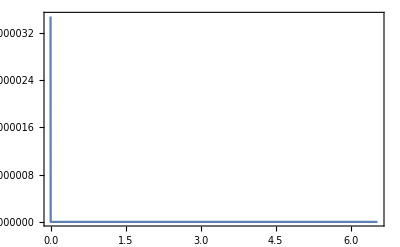

```mathematica
Plot[(1/M)*Psol/.{w->PercentGrowthConsumer1,ϕ->ScaledMassConsumer2},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,1],PlotRange->All]
```

```mathematica
(*detlist = ParallelTable[{10^i,Abs[Det[(JacobianFullModel/.{w->1,Sub->1}/.M->10^i)]]},{i,1,7,0.05}];
thresholdsize = detlist[[Position[detlist,_?(#==Min[detlist]&)][[1]][[1]]]][[1]]
OptPredMass[thresholdsize]
ListLogLogPlot[detlist]*)
```

Now look at results WITH SUBSIDIES

```mathematica
(*Show[{
LogLogPlot[{Table[(1/M)*Sub/.{ϵ->i},{i,0.1,2,0.1}]},{M,1,10^8},PlotStyle->ColorData[97,2],Frame->True],
LogLogPlot[(1/M)*CsolNoSubsidies,{M,1,10^8},Frame->True,PlotStyle->ColorData[97,1]]
}]

*)
```

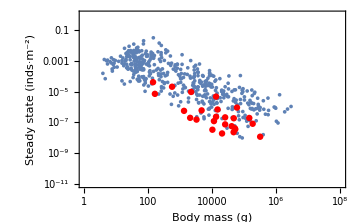

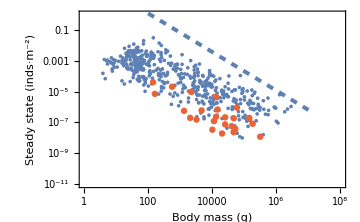

```mathematica
PercentGrowthConsumer=0.1; (*Percent with which the predator relies on the consumer for food*)
PercentSubsidyValue =0.6;
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->Red],
LogLogPlot[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,1]],
LogLogPlot[(1/M)*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},Frame->True,PlotStyle->ColorData[97,4]]
}]
MaxDensitiesPlot = Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (inds·m^-2)"},PlotRange->{10^-11,10^5},LabelStyle->Directive[FontSize->16]],
ListLogLogPlot[carnivoredata,PlotStyle->ColorData[97,4]],
LogLogPlot[(1/M)*PreyDensityTheoreticalMax[M]/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,1]}],
LogLogPlot[(1/M)*PredatorDensityTheoreticalMax[OptPredMass[M],M]/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,10,10^7},Frame->True,PlotStyle->{Thickness[0.008],Dashed,ColorData[97,4]}]
}]
```

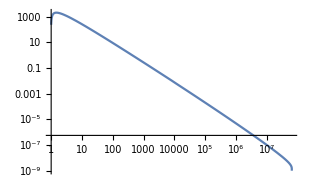

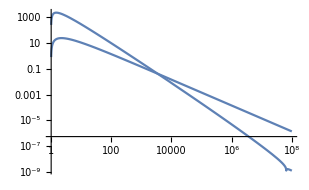

```mathematica
Show[{
LogLogPlot[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},PlotRange->All],
LogLogPlot[(1/M)*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue},{M,1,10^8},PlotRange->All]
}]
Show[{
LogLogPlot[Abs[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue}],{M,1,10^8},PlotRange->All],
LogLogPlot[Abs[(1/M)*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue}],{M,1,10^8}]
}]
```

```mathematica
(*ListLogLogPlot[Transpose[{Table[10^i,{i,0,8-0.01,0.01}],Differences[Table[Abs[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue}]/.M->10^i,{i,0,8,0.01}]]*Table[10^i,{i,0,8-0.01,0.01}]}],PlotRange->{{1,10^8},{0.0000000000001,All}}]
ListLogLogPlot[Transpose[{Table[10^i,{i,0,8-0.01,0.01}],Differences[Table[Abs[(1/M)*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue}]/.M->10^i,{i,0,8,0.01}]]*Table[10^i,{i,0,8-0.01,0.01}]}],PlotRange->{{1,10^8},{0.0000000000001,All}}]*)
```

```mathematica
iterator = 0.1;
diffC = Transpose[{Table[10^i,{i,0,8-0.01,0.01}],Differences[Table[Abs[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue}]/.M->10^i,{i,0,8,0.01}]]*Table[10^i,{i,0,8-0.01,0.01}]}];
intvecC = Intersection[Flatten[Position[diffC[[All,1]],_?((#>(10^4*(1+0.1))||#<(10^4*(1-0.1)))&)],1],
Flatten[Position[diffC[[All,2]],_?(#>0&)],1]];
thresholdpositionC = If[Length[intvecC]==0,Length[diffC],intvecC[[1]]];
thresholdsizeC =  diffC[[thresholdpositionC]][[1]]
diffP = Transpose[{Table[10^i,{i,0,8-0.01,0.01}],Differences[Table[Abs[(1/M)*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue}]/.M->10^i,{i,0,8,0.01}]]*Table[10^i,{i,0,8-0.01,0.01}]}];
intvecP = Intersection[Flatten[Position[diffP[[All,1]],_?((#>(10^4*(1+0.1))||#<(10^4*(1-0.1)))&)],1],
Flatten[Position[diffP[[All,2]],_?(#>0&)],1]];
thresholdpositionP = If[Length[intvecP]==0,Length[diffP],intvecP[[1]]];
thresholdsizeP =  diffP[[thresholdpositionP]][[1]]
```

1.

1.

```mathematica
(*PreySSMin=M/.N[(FindMinimum[{Abs[(1/M)*Csol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue}],{M>10001 &&M<10^8}},{M}])][[2]]
PredSSMin=M/.N[(FindMinimum[{Abs[(1/M)*Psol/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue}],{M<10000 }},{M}])][[2]]*)
```

```mathematica
(*(*PercentGrowthConsumer=0.9; (*Percent with which the predator relies on the consumer for food*)
PercentSubsidyValue =0.09;*)
detlist =ParallelTable[{10^i,Abs[Det[(JacobianFullModel/.{w->PercentGrowthConsumer,ϵ->PercentSubsidyValue}/.M->10^i)]]},{i,1,7,0.05}];
thresholdsize = detlist[[Position[detlist,_?(#==Min[detlist]&)][[1]][[1]]]][[1]]
OptPredMass[thresholdsize]
ListLogLogPlot[detlist]*)
```

Evaluate the herbivore and predator body size thresholds across different values of w and Sub

```mathematica
iterator = 0.1;
ThresholdsOverWEpsilon=Flatten[ParallelTable[
(*PreySSMin=M/.N[(FindMinimum[{Abs[(1/M)*Csol/.{w->wvalues,ϵ->epsilonvalues}],{M>10001 &&M<10^8}},{M}])][[2]];
PredSSMin=M/.N[(FindMinimum[{Abs[(1/M)*Psol/.{w->wvalues,ϵ->epsilonvalues}],{M<10000 }},{M}])][[2]];*)
diffC = Transpose[{Table[10^i,{i,0,7.5-0.01,0.01}],Differences[Table[Abs[(1/M)*Csol/.{w->wvalues,ϵ->10^epsilonvalues}]/.M->10^i,{i,0,7.5,0.01}]]*Table[10^i,{i,0,7.5-0.01,0.01}]}];
intvecC = Intersection[Flatten[Position[diffC[[All,1]],_?((#>(10^4*(1+0.1))||#<(10^4*(1-0.1)))&)],1],
Flatten[Position[diffC[[All,2]],_?(#>0&)],1]];
(*thresholdpositionC = If[Length[intvecC]==0,Length[diffC],intvecC[[1]]];
thresholdsizeC =  diffC[[thresholdpositionC]][[1]];*)
thresholdsizeC = If[Length[intvecC]==0,0,diffC[[intvecC[[1]]]][[1]]];
diffP = Transpose[{Table[10^i,{i,0,7.5-0.01,0.01}],Differences[Table[Abs[(1/M)*Psol/.{w->wvalues,ϵ->10^epsilonvalues}]/.M->10^i,{i,0,7.5,0.01}]]*Table[10^i,{i,0,7.5-0.01,0.01}]}];
intvecP = Intersection[Flatten[Position[diffP[[All,1]],_?((#>(10^4*(1+0.1))||#<(10^4*(1-0.1)))&)],1],
Flatten[Position[diffP[[All,2]],_?(#>0&)],1]];
(*thresholdpositionP = If[Length[intvecP]==0,Length[diffP],intvecP[[1]]];*)
(*thresholdsizeP =  diffP[[thresholdpositionP]][[1]];*)
thresholdsizeP = If[Length[intvecP]==0,0,diffP[[intvecP[[1]]]][[1]]];
{wvalues,10^epsilonvalues,thresholdsizeC,thresholdsizeP},
{wvalues,0.05,1,0.05},{epsilonvalues,-3.2,0.3,0.05}],1];
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/thresholdsoverwepsilon.csv"}],ThresholdsOverWEpsilon,"CSV"]
```

/Users/jdyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/data/thresholdsoverwepsilon.csv

```mathematica
ThresholdsOverWEpsilon = Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/data/thresholdsoverwepsilon.csv"}],"CSV"];
```

```mathematica
PreyThresholdMatrix = Transpose[{ThresholdsOverWEpsilon[[All,1]],ThresholdsOverWEpsilon[[All,2]],ThresholdsOverWEpsilon[[All,3]]}];
PredThresholdMatrix = Transpose[{ThresholdsOverWEpsilon[[All,1]],ThresholdsOverWEpsilon[[All,2]],ThresholdsOverWEpsilon[[All,4]]}];
PreySizeGapPos=Flatten[Position[ThresholdsOverWEpsilon[[All,3]],_?(#>1000&&#<10000&)],1];
PredSizeGapPos=Flatten[Position[ThresholdsOverWEpsilon[[All,4]],_?(#>1000&&#<10000&)],1];
PreyTM=PreyThresholdMatrix[[PreySizeGapPos,1;;2]];
PredTM=PreyThresholdMatrix[[PredSizeGapPos,1;;2]];
```

```mathematica
Max[PredThresholdMatrix[[All,3]]]
```

954993.

```mathematica
N[10^(7.5)]
```

3.16228×10^7

```mathematica
ThresholdPlot=GraphicsRow[{
Show[{
ListContourPlot[PreyThresholdMatrix,FrameLabel->{"% Growth from Herbivore (w)","Fraction Subsidy Density (ϵ)"},ScalingFunctions->{None,"Log","Log"},FrameTicks->Automatic,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{10,5}},LegendLabel->"C Density",LabelStyle->{Italic,FontFamily->"Times New Roman",FontSize->14},LegendMarkerSize->200],Right],ImageSize->300,LabelStyle->Directive[FontSize->16]],
(*ListLogPlot[PreyThresholdMatrix[[PreySizeGapPos,1;;2]],PlotStyle->Black],*)
Graphics[{ColorData[97,5],Opacity[0.8],ConcaveHullMesh[Transpose[{PreyTM[[All,1]],Log@PreyTM[[All,2]]}]]}]
}],
Show[{
ListContourPlot[PredThresholdMatrix,FrameLabel->{"% Growth from Herbivore (w)","Fraction Subsidy Density (ϵ)"},ScalingFunctions->{None,"Log","Log"},FrameTicks->Automatic,PlotLegends->Placed[BarLegend[Automatic,LegendMargins->{{0,0},{5,5}},LegendLabel->"P Density",LabelStyle->{Italic,FontFamily->"Times New Roman",FontSize->14},LegendMarkerSize->200],Right],ImageSize->300,LabelStyle->Directive[FontSize->16]],
(*ListLogPlot[PredThresholdMatrix[[PredSizeGapPos,1;;2]],PlotStyle->Black],*)
Graphics[{ColorData[97,5],Opacity[0.8],ConcaveHullMesh[Transpose[{PredTM[[All,1]],Log@PredTM[[All,2]]}]]}]
}]
},ImageSize->800,Spacings->0]
```

-Graphics-

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_thresholdsoverwepsilon.pdf"}],ThresholdPlot,"PDF"]
```

/Users/jdyeakel/Dropbox/PostDoc/2022_PredatorConsumerResource/figures/fig_thresholdsoverwepsilon.pdf